# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 7 - Quantum Theory of Solids

## 7.1 THEORY

### 7.1.1 Linear chain

```mathematica
lineHamiltonian[nSites_]:=Table[
KroneckerDelta[r,s-1]+KroneckerDelta[r,s+1]
,{r,1,nSites},{s,1,nSites}]
```

```mathematica
ArrayPlot[ lineHamiltonian[6] ]
```

-Graphics-

### 7.1.2 Periodic boundary conditions

```mathematica
ringHamiltonian[nSites_]:=Table[
KroneckerDelta[r,s-1]+KroneckerDelta[r,s+1]+KroneckerDelta[r,1]*KroneckerDelta[s,nSites]+KroneckerDelta[r,nSites]*KroneckerDelta[s,1]
,{r,1,nSites},{s,1,nSites}]
```

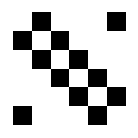

```mathematica
ArrayPlot[ ringHamiltonian[6] ]
```

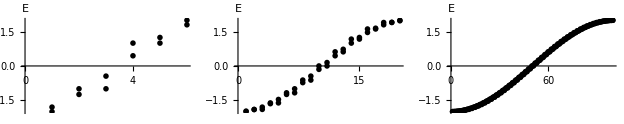

```mathematica
ringLineComparison[n_,t_:-1.0]:=ListPlot[
{Eigenvalues[t*ringHamiltonian[n]]//Sort,Eigenvalues[t*lineHamiltonian[n]]//Sort},
AxesLabel->{" ","E"}]

GraphicsRow[
{ringLineComparison[6],
ringLineComparison[20],
ringLineComparison[100]} ] (*Erratum (first printing): p. 182, argument is 100 *)
```

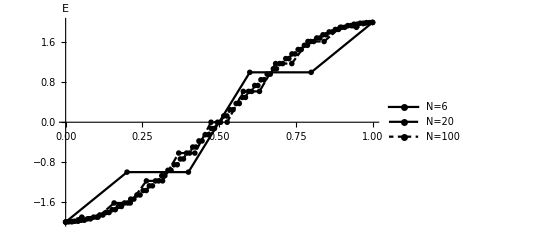

```mathematica
t=-1.0;
ListPlot[
{Eigenvalues[t*ringHamiltonian[6]]//Sort,Eigenvalues[t*ringHamiltonian[20]]//Sort,Eigenvalues[t*ringHamiltonian[100]]//Sort},
DataRange->{0,1},
Joined->True,AxesLabel->{"","E"},
PlotLegends->{"N=6","N=20","N=100"}]
```

## 7.3 EXAMPLES

### 7.3.1 Polyacetylene

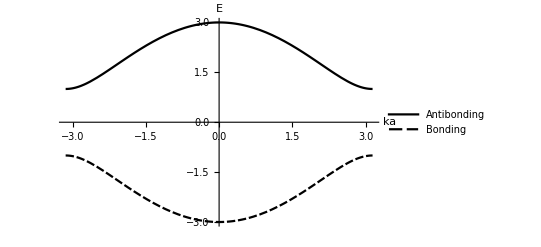

```mathematica
E0=0;t1=-2;t2=-1;
Plot[
{E0+Sqrt[t1^2+t2^2+2*t1*t2*Cos[ka]],
E0-Sqrt[t1^2+t2^2+2*t1*t2*Cos[ka]] },
{ka,-Pi,+Pi},AxesLabel->{"ka","E"},
PlotLegends->{"Antibonding","Bonding"} ]
```

```mathematica
E0 = 0; t1 = -2; t2 = -1;
hMatr=({{E0, t1+t2*Exp[-I*ka]}, {t1+t2*Exp[+I*ka], E0}});
evals=Eigenvalues[hMatr]
evecs=Eigenvectors[hMatr]
```

{-ⅇ^(-(ⅈ ka)/2) √(2+5 ⅇ^(ⅈ ka)+2 ⅇ^(2 ⅈ ka)),ⅇ^(-(ⅈ ka)/2) √(2+5 ⅇ^(ⅈ ka)+2 ⅇ^(2 ⅈ ka))}

{{(ⅇ^(-(ⅈ ka)/2) √(2+5 ⅇ^(ⅈ ka)+2 ⅇ^(2 ⅈ ka)))/(2+ⅇ^(ⅈ ka)),1},{-(ⅇ^(-(ⅈ ka)/2) √(2+5 ⅇ^(ⅈ ka)+2 ⅇ^(2 ⅈ ka)))/(2+ⅇ^(ⅈ ka)),1}}

Erratum (first printing):  First line of code output is misprinted

```mathematica
evals/.ka->0
evecs/.ka->0
```

{-3,3}

{{1,1},{-1,1}}

```mathematica
evals/.ka->Pi/2 //FullSimplify
evecs/.ka->Pi/2 //FullSimplify
```

{-√5,√5}

{{(2-ⅈ)/(√5),1},{-(2-ⅈ)/(√5),1}}

### 7.3.2 Polyacene

```mathematica
t=-2.7; (*C-C nearest-neighbor Huckel parameter, in eV*)
Hrr = t*({{0, 1, 0, 0}, {1, 0, 1, 0}, {0, 1, 0, 1}, {0, 0, 1, 0}});
Hright = t*Exp[+I*ka]*({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}});
```

```mathematica
Eigenvalues[((Hrr+Hright+ConjugateTranspose[Hright])/.ka->0)]//Sort
```

{-6.91619,-4.21619,4.21619,6.91619}

```mathematica
bandList={{},{},{},{}};
Do[(*loop over values of ka*)currentEvals=Eigenvalues[N[((Hrr+Hright+ConjugateTranspose[Hright])/.ka->kaval)]
]//Sort//Chop;
Do[(*loop over bands;append each band to corresponding bandList*)
AppendTo[bandList[[i]],{kaval/Pi,currentEvals[[i]]}];,{i,1,Length[currentEvals]}
];
,{kaval,0,+Pi,0.01}];
```

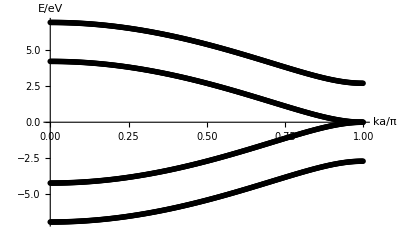

```mathematica
ListPlot[bandList,
Joined->True,AxesLabel->{"ka/π","E/eV"}]
```

## 7.4 DERIVED PROPERTIES

### 7.4.2 Density of states

```mathematica
calcDOS[bandList_,dE_]:=Module[
{DOS={},nStates},
Do[(*loop over energy range*)
nStates=0;
Do[(*loop over bands and count states near this energy value*)If[energy-dE/2≤bandList[[i,j,2]]<energy+dE/2,nStates++];
,{j,Length[bandList[[1]]]},{i,Length[bandList]}];AppendTo[DOS,{energy,nStates/dE}];
,{energy,Min[bandList]-dE,Max[bandList]+dE,dE}];
DOS
];
```

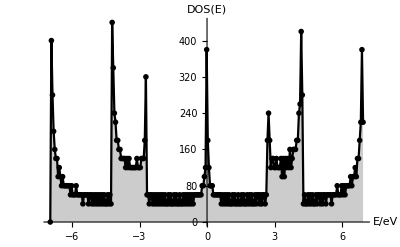

```mathematica
ListPlot[ calcDOS[bandList,0.05],Joined->True,
Filling->Axis,PlotRange->All,AxesLabel->{"E/eV","DOS(E)"}]
```

### 7.4.3 Total energy

```mathematica
calcTotalEnergy[occupiedBands_]:=Sum[Sum[occupiedBands[[i,j,2]],{i,Length[occupiedBands]}]
,{j,Length[occupiedBands[[1]]]}]/Length[occupiedBands[[1]]]
```

```mathematica
calcTotalEnergy[bandList[[1;;2]]]
```

-7.57568

### 7.4.4 Effective mass

```mathematica
effectiveMass[bandData_,energy2Hartree_]:=Module[
{EM=bandData,(*copy the band information to get the k values*)
dk2=(bandData[[2,1]]-bandData[[1,1]])^2,(*constant delta-k*)
nk=Length[bandData]},(*number of k values in the list*)
Do[
EM[[i,2]]=dk2/(energy2Hartree*
(bandData[[i+1,2]]-2*bandData[[i,2]]+bandData[[i-1,2]]));
,{i,2,nk-1}];(*handle "edges" in k separately below*)

EM[[1,2]]=dk2/(energy2Hartree*
(bandData[[2,2]]-2*bandData[[1,2]]+bandData[[2,2]]));
EM[[nk,2]]=dk2/(energy2Hartree*
(bandData[[nk-1,2]]-2*bandData[[nk,2]]+bandData[[nk-1,2]]));
EM
];
```

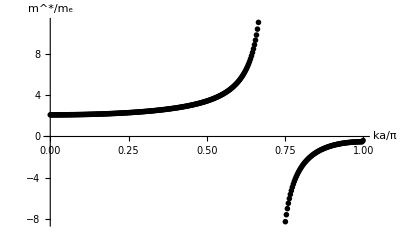

```mathematica
ListPlot[ effectiveMass[bandList[[2]],1/27.2117],
AxesLabel->{"ka/π ","m^*/m_e"}]
```